```mathematica
x1[t_]=x[t]/.NDSolve[{x''[t]+4 Sin[x[t]]-1/2 (x[t])^3==0,x[0]==0,x'[0]==2.7},x[t],{t,0,10}][[1]]
```

InterpolatingFunction[…][t]

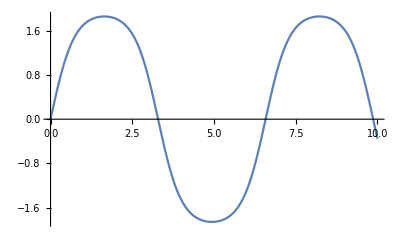

```mathematica
Plot[x1[t],{t,0,10}]
```

```mathematica
t1=t/.FindRoot[x1[t]==0,{t,0}]
```

0.

```mathematica
t2=t/.FindRoot[x1[t]==0,{t,Pi}]
```

3.28928

```mathematica
t3=t/.FindRoot[x1[t]==0,{t,2 Pi}]
```

6.57856

```mathematica
t4=t/.FindRoot[x1[t]==0,{t,3 Pi}]
```

9.86784

```mathematica
FindMaximum[x1[t],{t,8}]
```

{1.86057,{t→8.2232}}

```mathematica
t3-t1
```

6.57856

```mathematica
Accuracy[t3]
```

15.1365